```mathematica
f=Function[x,Sin[x]]
g=Function[x,1/x^2]
h=Function[x,Log[x]]
f[g[h[x]]]==0
```

Function[x,Sin[x]]

Function[x,1/x^2]

Function[x,Log[x]]

Sin[1/Log[x]^2]==0

To solve f(g(h(x))) = k, we must first solve f(u) = k for u, then solve g(v) = u for v for all inputs u, and then solve h(w) = v for w for all v. w are the solutions that solve f(g(h(x))) = k

```mathematica
uValues=DeleteCases[Flatten[x/.NSolve[Sin[x]==0&&0<x<26]],0.]
vValues=Flatten[DeleteCases[x/.Solve[1/x^2==#, x, Reals]&/@uValues,x]]
wValues=Flatten[x/.Solve[Log[x]==#]&/@vValues]
```

{3.14159,6.28319,9.42478,12.5664,15.708,18.8496,21.9911,25.1327}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{-0.56419,0.56419,-0.398942,0.398942,-0.325735,0.325735,-0.282095,0.282095,-0.252313,0.252313,-0.230329,0.230329,-0.213244,0.213244,-0.199471,0.199471}

{0.568821,1.75802,0.671029,1.49025,0.721996,1.38505,0.754202,1.3259,0.777001,1.287,0.794272,1.25901,0.807959,1.23769,0.819164,1.22076}

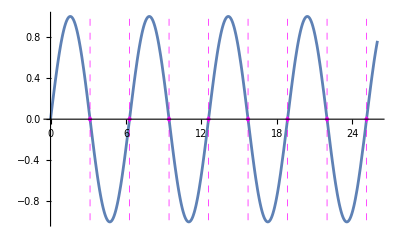

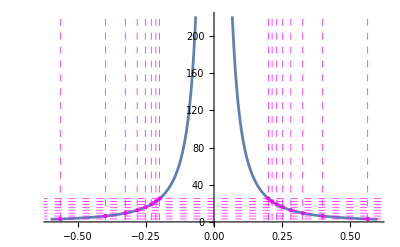

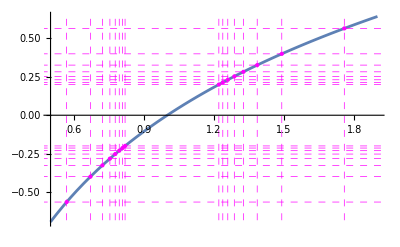

```mathematica
Plot[f[x],
{x,0,26},
GridLines->{uValues},
GridLinesStyle->Directive[Thickness[Small],Magenta, Dashed],
MeshFunctions->{Function[{x,y},y]},
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},
MeshStyle->Directive[PointSize@Medium,Magenta]]
Plot[g[x],
{x,-0.6,0.6},
GridLines->{vValues, uValues},
GridLinesStyle->Directive[Thickness[Small],Magenta, Dashed],
MeshFunctions->{Function[{x,y},y]},
Mesh->{uValues},
MeshStyle->Directive[PointSize@Medium,Magenta]]
Plot[h[x],
{x,0.5,1.9},
GridLines->{wValues,vValues},
GridLinesStyle->Directive[Thickness[Small],Magenta, Dashed],
MeshFunctions->{Function[{x,y},y]},
MeshFunctions->{Function[{x,y},y]},
Mesh->{vValues},
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

The graphs here show the solving process as f(u) = k = 0 is first solved in the top graph for values of u. Then these u values are used to solve g(v) = u, which is shown in the second graph. The solutions are v values which are then used to solve h(w) = v, which is shown in the last graph.

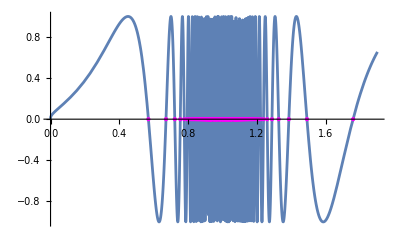

```mathematica
Plot[f[g[h[x]]],
{x,0,1.9},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

The current solutions shown in the graphs above are the solutions where u in f(u)=k=0 ranges from 0 to 26. As you increase the upper bound, the solutions clump up at 1. As shown in the last graph the solutions seem to be approaching 1 and the density of solutions increasing as it gets closer to 1.